```mathematica
双光栅实验,未编号
```

```mathematica
双光栅振动测量共振曲线
```

{fm→29483.4,ω0→3182.47,b→0.980457}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{9.44897,{ω→3182.47}}

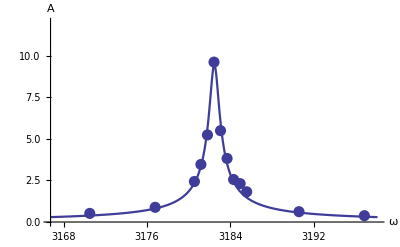

```mathematica
t={504.6,0.5173,505.6,0.8836,506.2,2.435,
506.3,3.462,506.4,5.236,506.5,9.615,506.6,
5.493,506.7,3.822,506.8,2.554,506.9,2.308,
507.0,1.816,507.8,0.6205,508.8,0.3803};
t=Partition[t,2];len=Length[t];
t=Table[{2π*t[[i,1]],t[[i,2]]},{i,len}];
g1=ListPlot[t,PlotStyle->PointSize[0.02]];
fit=FindFit[t,fm/(√((ω0^2-ω^2)^2+b^2*ω^2)),
{{fm,1900},{ω0,3187},{b,0.01}},ω]
FindMaximum[fm/(√((ω0^2-ω^2)^2+b^2*ω^2))/.fit,
{ω,2π*506.5}]
g2=Plot[fm/(√((ω0^2-ω^2)^2+b^2*ω^2))/.fit,
{ω,2 π*504,2 π*509},PlotRange->All,
PlotStyle->Thickness[0.004]];
Show[{g1,g2},AxesStyle->Thickness[0.003],
AxesLabel->{"ω","A"},AxesOrigin->{2 π*504,0},
PlotRange->{{2 π*504,2 π*509},{0,12}}]
Clear[t,len,b,fm,ω,ω0,g1,g2,fit]
```

```mathematica
另一次测量
```

{fm→262991.,ω0→3182.96,b→1.27331}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{64.8897,{ω→3182.96}}

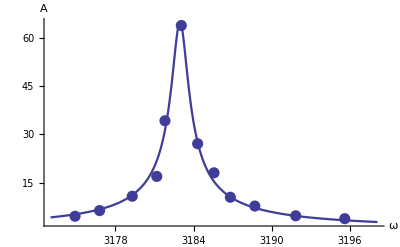

```mathematica
t={505.3,4.51,505.6,6.275,506,10.75,506.3,
16.92,506.4,34.26,506.6,63.93,506.8,27.105,
507.0,18.045,507.2,10.425,507.5,7.68,508,
4.65,508.6,3.75};
t=Partition[t,2];len=Length[t];
t=Table[{2π*t[[i,1]],t[[i,2]]},{i,len}];
g1=ListPlot[t,PlotStyle->PointSize[0.02]];
fit=FindFit[t,fm/(√((ω0^2-ω^2)^2+b^2*ω^2)),
{{fm,1900},{ω0,3187},{b,1}},ω]
FindMaximum[fm/(√((ω0^2-ω^2)^2+b^2*ω^2))/.fit,
{ω,2π*506.4}]
g2=Plot[fm/(√((ω0^2-ω^2)^2+b^2*ω^2))/.fit,
{ω,2 π*505,2 π*509},PlotRange->All,
PlotStyle->Thickness[0.004]];
Show[{g1,g2},AxesLabel->{"ω","A"},
AxesOrigin->{2 π*505,0},
AxesStyle->Thickness[0.003],
PlotRange->{{2 π*505,2 π*509},All}]
Clear[t,len,b,fm,ω,ω0,g1,g2,fit]
```

```mathematica
改小0.1Hz
```

{fm→246505.,ω0→3182.97,b→0.544054}

{142.348,{ω→3182.97}}

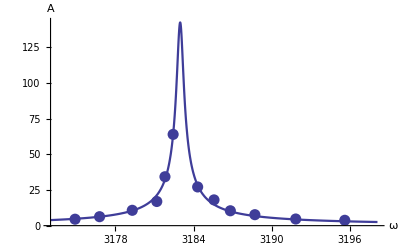

```mathematica
t={505.3,4.51,505.6,6.275,506,10.75,506.3,
16.92,506.4,34.26,506.5,63.93,506.8,27.105,
507.0,18.045,507.2,10.425,507.5,7.68,508,
4.65,508.6,3.75};
t=Partition[t,2];len=Length[t];
t=Table[{2π*t[[i,1]],t[[i,2]]},{i,len}];
g1=ListPlot[t,PlotStyle->PointSize[0.02]];
fit=FindFit[t,fm/(√((ω0^2-ω^2)^2+b^2*ω^2)),
{{fm,1900},{ω0,3187},{b,1}},ω]
FindMaximum[fm/(√((ω0^2-ω^2)^2+b^2*ω^2))/.fit,
{ω,2π*506.4}]
g2=Plot[fm/(√((ω0^2-ω^2)^2+b^2*ω^2))/.fit,
{ω,2 π*505,2 π*509},PlotRange->All,
PlotStyle->Thickness[0.004]];
Show[{g1,g2},AxesStyle->Thickness[0.003],
AxesLabel->{"ω","A"},
PlotRange->{{2 π*505,2 π*509},All},
AxesOrigin->{2 π*505,0}]
Clear[t,len,b,fm,ω,ω0,g1,g2,fit]
```

```mathematica
改大0.1Hz
```

{fm→250522.,ω0→3183.06,b→9.27212×10^-8}

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{8.4883×10^8,{ω→3183.06}}

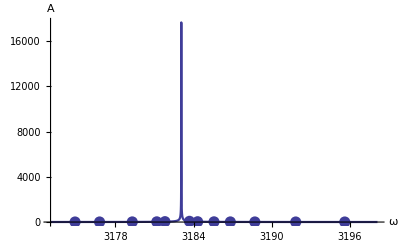

```mathematica
t={505.3,4.51,505.6,6.275,506,10.75,506.3,
16.92,506.4,34.26,506.7,63.93,506.8,27.105,
507.0,18.045,507.2,10.425,507.5,7.68,508,
4.65,508.6,3.75};
t=Partition[t,2];len=Length[t];
t=Table[{2π*t[[i,1]],t[[i,2]]},{i,len}];
g1=ListPlot[t,PlotStyle->PointSize[0.02]];
fit=FindFit[t,fm/(√((ω0^2-ω^2)^2+b^2*ω^2)),
{{fm,1900},{ω0,3187},{b,1}},ω]
FindMaximum[fm/(√((ω0^2-ω^2)^2+b^2*ω^2))/.fit,
{ω,2π*506.4}]
g2=Plot[fm/(√((ω0^2-ω^2)^2+b^2*ω^2))/.fit,
{ω,2 π*505,2 π*509},PlotRange->All,
PlotStyle->Thickness[0.004]];
Show[{g1,g2},AxesStyle->Thickness[0.003],
AxesLabel->{"ω","A"},
PlotRange->{{2 π*505,2 π*509},All},
AxesOrigin->{2 π*505,0}]
Clear[t,len,b,fm,ω,ω0,g1,g2,fit]
```